# Call Python to compute CY metrics

The easiest thing to get started would be to just run the entire notebook

In order to install the program, you just need to call Setup[] (Setup will detect whether you have run it before and not do anything if everything is already setup; so it does not hurt to just compile the entire notebook every time). Setup[] will try to discover python3 on your system and create a virtual environment with all required packages installed. For some combinations of Python and Mathematica versions, setup will automatically apply a bug fix. 

If you want to see the Documentation for any of the functions, run e.g. ?TrainNN. Running Options[TrainNN] gives you a list of the options for this function and their default values.

More advanced (if you do not want to just call Setup[] and be done with it):
1.)If you already have a python environment that you want to use, you need to “pip install --user pyzmq” for it to work with Mathematica.  
2.) Then setup the package to use this python interpreter with ChangeSetting[“Python”,”<path/to/python>”].

## Setup Python for CY metrics

Load the package for the web.
You can also download the package file and copy it to Mathematica’s Application folder. Too find the folder execute the following command in Mathematica: FileNameJoin[{$UserBaseDirectory,”/Applications”}] 
Then just copy the file https://github.com/pythoncymetric/cymetric/tree/main/cymetric/wolfram/cymetric.m to this directory and run with <<cymetric`

```mathematica
NotebookEvaluate["https://raw.githubusercontent.com/pythoncymetric/cymetric/main/cymetric/wolfram/cymetric.m"]
```

```mathematica
python=Setup["~/Desktop/mathematica_venv"];
(*If you already have an environment that you want to use, set the path here*)
(*ChangeSetting["Python","<path/to/python>"]*)
```

## Quintic

### Compute Points and Metric

```mathematica
?GeneratePoints
Options[GeneratePoints]
```

{KahlerModuli→{},Points→200000,Precision→20,VolJNorm→1,Python→Null,Session→Null,Dir→/Users/ruehle/GitHub/su3-metric/mathematica_integration/test,Verbose→3}

```mathematica
outDir=FileNameJoin[{NotebookDirectory[],"QuniticPsi0"}];
```

```mathematica
poly={Subscript[z, 0]^5+Subscript[z, 1]^5+Subscript[z, 2]^5+Subscript[z, 3]^5+Subscript[z, 4]^5+0 Subscript[z, 0] Subscript[z, 1] Subscript[z, 2] Subscript[z, 3] Subscript[z, 4]};
{res,session}=GeneratePoints[poly,{4},"Points"->5000,"KahlerModuli"->{1},"Dir"->outDir,"VolJNorm"->5];
```

Warning: No variables specified, assuming alphabetical monomial ordering.

Variables have been assigned to the ambient space factors as follows:

1.) P^4: {z_0,z_1,z_2,z_3,z_4}

Generating 5000 points...

Configuration matrix: {{5}}

Number of Parameters per P^n: {1}

Number of points on CY from one ambient space intersection: 5

Now generating 5000 points...

done.

Writing points to /Users/ruehle/GitHub/su3-metric/mathematica_integration/QuniticPsi0/points.pickle

DEBUG:mathematica:Using output directory /Users/ruehle/GitHub/su3-metric/mathematica_integration/QuniticPsi0

DEBUG:mathematica:Ambient space: P^4

DEBUG:mathematica:Kahler moduli: [1]

DEBUG:mathematica:{'outdir': '/Users/ruehle/GitHub/su3-metric/mathematica_integration/QuniticPsi0', 'logger_level': 10, 'num_pts': 5000, 'monomials': array([[[5, 0, 0, 0, 0],

[0, 5, 0, 0, 0],

[0, 0, 5, 0, 0],

[0, 0, 0, 5, 0],

[0, 0, 0, 0, 5]]]), 'coeffs': array([[1, 1, 1, 1, 1]]), 'k_moduli': array([1]), 'ambient_dims': array([4]), 'precision': 20, 'vol_j_norm': 5, 'selected_t': array([1]), 'point_file_path': '/Users/ruehle/GitHub/su3-metric/mathematica_integration/QuniticPsi0/points.pickle'}

INFO:mathematica:Saving point generator to /Users/ruehle/GitHub/su3-metric/mathematica_integration/QuniticPsi0/point_gen.pickle

INFO:mathematica:Computing derivatives of J_FS, Omega, ...

DEBUG:mathematica:done

```mathematica
{history,session}=TrainNN["HiddenLayers"->{64,64,64},"ActivationFunctions"->{"gelu","gelu","gelu"},"Epochs"->3,"BatchSize"->64,"Session"->session,"Dir"->outDir,"Verbose"->3];
```

{
        'outdir':        "/Users/ruehle/GitHub/su3-metric/mathematica_integration/QuniticPsi0",
        'logger_level':  logging.DEBUG,
        'model':         "MultFS",
        'callbacks':     False,
        'n_hiddens':     [64, 64, 64],
		'acts':          ["gelu", "gelu", "gelu"],
		'n_epochs':      3,
		'batch_size':    64,
		'kappa':         0.,
        'alphas':        [1., 1., 1., 1., 1.],
        'toric_data_path':""
       }

DEBUG:mathematica:Using CPU for computation.

DEBUG:mathematica:Model: "sequential"

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:Layer (type)                 Output Shape              Param #

DEBUG:mathematica:=================================================================

DEBUG:mathematica:dense (Dense)                (None, 64)                704

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:dense_1 (Dense)              (None, 64)                4160

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:dense_2 (Dense)              (None, 64)                4160

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:dense_3 (Dense)              (None, 9)                 585

DEBUG:mathematica:=================================================================

DEBUG:mathematica:Total params: 9,609

DEBUG:mathematica:Trainable params: 9,609

DEBUG:mathematica:Non-trainable params: 0

DEBUG:mathematica:_________________________________________________________________

Epoch 1/3

71/71 - 33s - sigma_loss: 3.8513 - kaehler_loss: 0.0149 - transition_loss: 0.0103 - volk_loss: 1.4463e-05

Epoch 2/3

71/71 - 1s - sigma_loss: 0.2713 - kaehler_loss: 0.0107 - transition_loss: 0.0112 - volk_loss: 8.6629e-07

Epoch 3/3

71/71 - 1s - sigma_loss: 0.2201 - kaehler_loss: 0.0072 - transition_loss: 0.0104 - volk_loss: 8.1497e-07

Writing training information to /Users/ruehle/GitHub/su3-metric/mathematica_integration/QuniticPsi0/training_history_mathematica.m

```mathematica
{pts,session}=GetPoints["all","Dir"->outDir];
```

```mathematica
{weights,session}=GetFSWeights["all","Dir"->outDir];
```

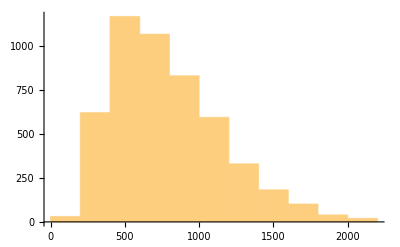

```mathematica
Histogram[weights]
```

```mathematica
{metrics, session}=CYMetric[pts[[1;;10]],"Dir"->outDir];
```

```mathematica
metrics[[1,2]]//Chop//MatrixForm
```

(0.0429216 | 0.000842249-0.000130305 ⅈ | -0.000801277+0.000122889 ⅈ
0.000842249+0.000130305 ⅈ | -0.04292+5.35636×10^-10 ⅈ | -0.000255717-0.000021872 ⅈ
-0.000801277-0.000122889 ⅈ | -0.000255717+0.0000218719 ⅈ | -0.0349957)

### Plot losses

```mathematica
history
```

<|sigma_loss→{0.778016,0.351312,0.304831},kaehler_loss→{0.000958132,0.00224807,0.00389013},transition_loss→{0.00295141,0.00363773,0.00434242},volk_loss→{0.0000238469,0.0000147296,0.0000157204}|>

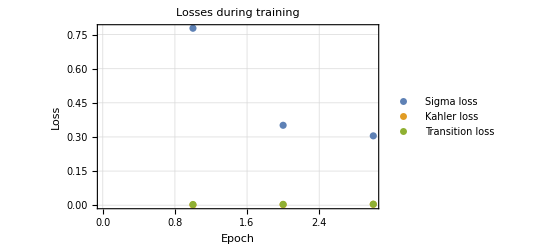

```mathematica
ListPlot[{history[["sigma_loss"]],history[["kaehler_loss"]],history[["transition_loss"]]},PlotLabel->"Losses during training",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

```mathematica
ListPlot[{history[["sigma_val"]],history[["kaehler_val"]],history[["transition_val"]]},PlotLabel->"Losses on validation set",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
ListPlot[{history[["sigma_val"]],history[["ricci_val"]]},PlotLabel->"Sigma and Ricci loss",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Ricci loss"},PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
SigmaVsRicci=Table[{history[["sigma_val"]][[i]],history[["ricci_val"]][[i]]},{i,Length[history[["sigma_val"]]]}];
```

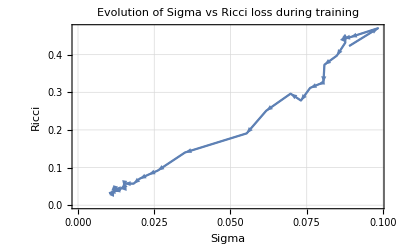

```mathematica
Show@@Join[{ListLinePlot[SigmaVsRicci,PlotLabel->"Evolution of Sigma vs Ricci loss during training",AxesLabel->{"Sigma","Ricci"},PlotTheme->"Detailed"]},Table[ListLinePlot[SigmaVsRicci[[i;;i+1]],PlotStyle->Directive[Thick,Arrowheads[.035]]]/.Line->Arrow,{i,Length[SigmaVsRicci]-1}]]
```

### Use trained NN to compute metrics and check improvement of Monge-Ampere equation

```mathematica
pts[[1]]
```

{-0.362437+0.691992 ⅈ,1.,0.416867+0.363721 ⅈ,-0.356542-0.879051 ⅈ,-0.232024+0.494326 ⅈ}

```mathematica
{pts,session}=GetPoints["val","Session"->session,"Dir"->outDir];
```

```mathematica
{gCYs[[1,1]]->MatrixForm[gCYs[[1,2]]]}//Chop
```

{{-0.289608+0.77897 ⅈ,1.,0.671475+0.568155 ⅈ,-0.503197-0.101559 ⅈ,-0.0516756+0.79406 ⅈ}→(0.188079-2.84443×10^-10 ⅈ | 0.0094713+0.00386941 ⅈ | 0.0170434+0.0538776 ⅈ
0.0094713-0.00386941 ⅈ | 0.0956125 | 0.0154819+0.0113262 ⅈ
0.0170434-0.0538776 ⅈ | 0.0154819-0.0113262 ⅈ | 0.114849)}

```mathematica
Eigenvalues[gCYs[[1,2]]]//Re//Chop
```

{0.2214,0.101416,0.0757234}

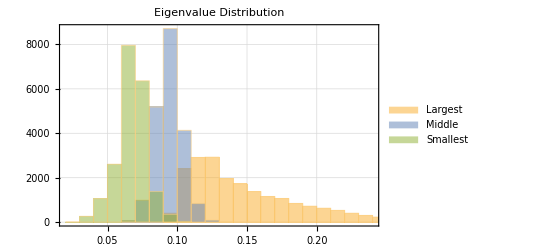

```mathematica
EigVals=Table[Eigenvalues[gCYs[[i,2]]]//Re//Chop,{i,Length[gCYs]}];
Histogram[{EigVals[[;;,1]],EigVals[[;;,2]],EigVals[[;;,3]]},PlotLabel->"Eigenvalue Distribution",PlotTheme->"Detailed",ChartLegends->{"Largest", "Middle","Smallest"}]
```

```mathematica
{weightsCY,session}=GetCYWeights["val","Session"->session,"Dir"->outDir];
{weightsFS,session}=GetFSWeights["val","Session"->session,"Dir"->outDir];
```

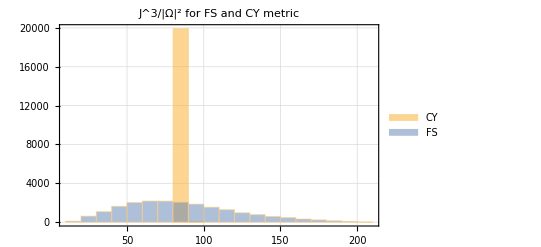

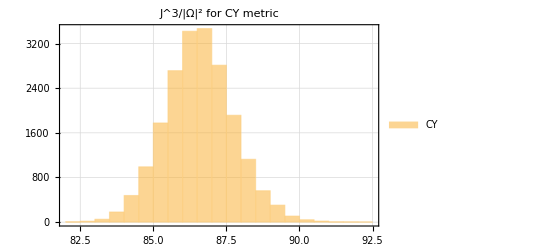

```mathematica
Histogram[{weightsCY,weightsFS},PlotLabel->"J^3/|Ω|^2 for FS and CY metric",PlotTheme->"Detailed",ChartLegends->{"CY", "FS"}]
Histogram[{weightsCY},PlotLabel->"J^3/|Ω|^2 for CY metric",PlotTheme->"Detailed",ChartLegends->{"CY"}]
```